# One Postulate in Wolfram

This notebook is a public-facing computational companion to the local paper and Lean development. It follows the paper's narrative arc while keeping the proofs in Lean.

It is not a proof-assistant notebook and not a raw symbolic scratchpad. Its job is to compute and visualize the kappa-family clearly enough that a non-Lean reader can see why the Killing form is the pivot.

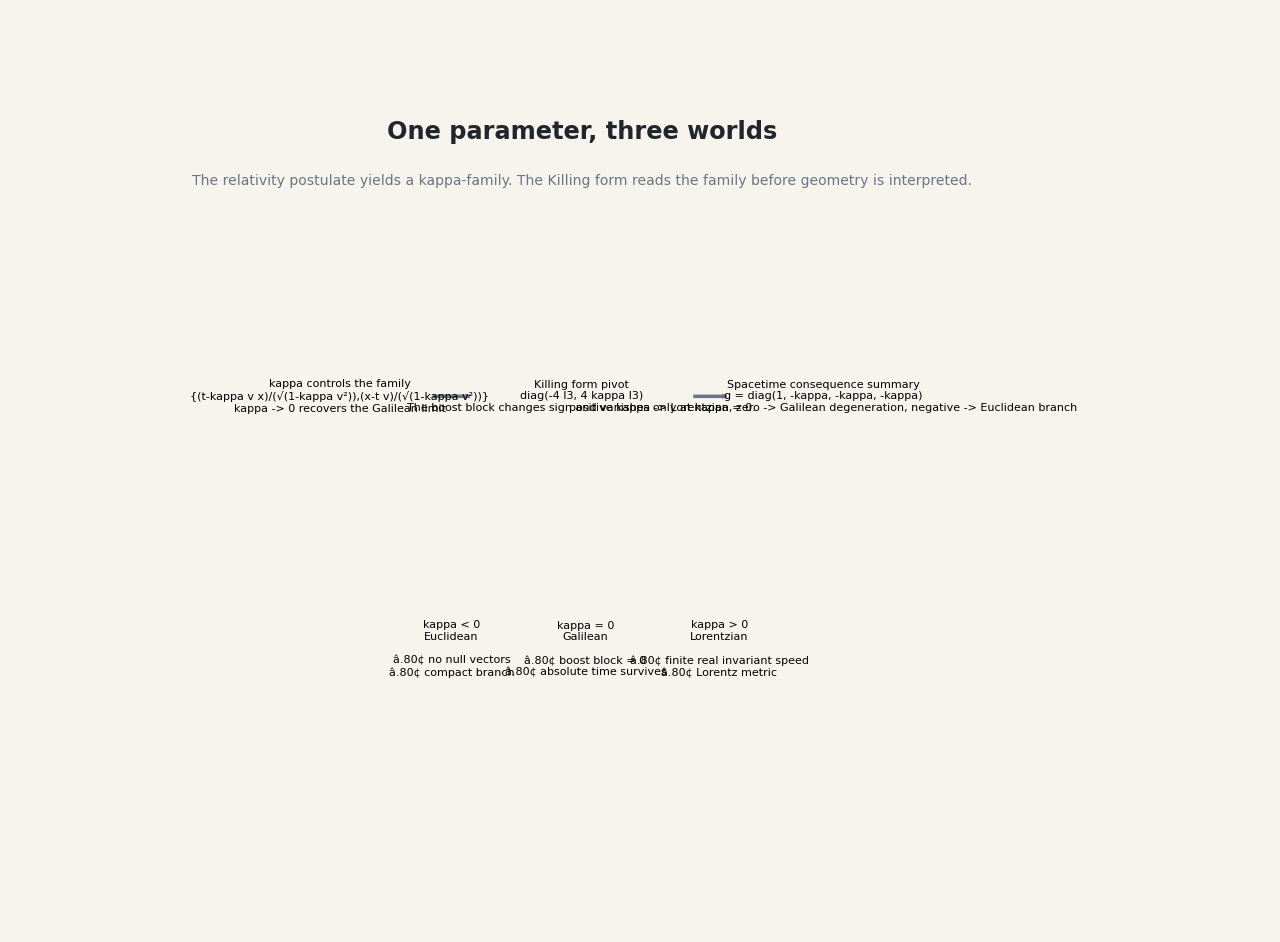
-Graphics-
Hero overview. One parameter controls the transformation family, the Killing form reads the branch structure, and the spacetime consequences follow afterward.

## What this notebook is for

Computed or visualized here means: Wolfram evaluates exact limits, matrix formulas, determinants, congruence calculations, and visual summaries of formulas already present in the paper and Lean files.

Formally proved in Lean means: theorem names and proof-structure claims come from local Lean modules, not from Wolfram. Interpretive framing comes from the paper.

## One parameter, three worlds

The paper's starting point is a single kappa-controlled family of inertial-frame transformations. The sign of kappa is not interpreted first; the notebook computes the shared structure and then reads the branch split from the invariant form.

-Graphics-
Branch overview. The same symbolic family produces Lorentzian, Galilean, and Euclidean regimes depending only on the sign of kappa.

Selected kappa | 1/2
Branch | Lorentzian branch
gamma(v) | 1/(√(1-v^2/2))
Galilean limit | {t,x-t v}

## The transformation law and the Galilean limit

These are the same formulas stated in the paper: gamma controls the boost family, time-space mixing is scaled by kappa, and the Galilean case appears as the exact kappa -> 0 limit.

```mathematica
1/(√(1-kappa v^2))
```

1/(√(1-kappa v^2))

```mathematica
(t-kappa v x)/(√(1-kappa v^2))
```

(t-kappa v x)/(√(1-kappa v^2))

```mathematica
(-t v+x)/(√(1-kappa v^2))
```

(-t v+x)/(√(1-kappa v^2))

```mathematica
1
```

1

```mathematica
{t,-t v+x}
```

{t,-t v+x}

## The kinematic bracket family

The bracket table below matches the local Lean conventions: rotations close among themselves, rotations send boosts to boosts, and the boost commutator scales as -kappa times a rotation.

Bracket | Exact local formula
[J_i, J_j] | Sum_k epsilon_ijk J_k
[J_i, K_j] | Sum_k epsilon_ijk K_k
[K_i, K_j] | Sum_k (-(kappa) epsilon_ijk) J_k

```mathematica
{{-kappa,0,0},{0,-kappa,0},{0,0,-kappa}}
```

{{-kappa,0,0},{0,-kappa,0},{0,0,-kappa}}

That boost block scaling is the local computational shadow of `boostCommutator_scales_with_kappa` in `OnePostulate/KinematicAlgebra.lean`.

## Computing the Killing form

The decisive invariant is computed before any geometry is interpreted. In the local Lean development this is `killing_form_diag` and `boost_killing_form_eq`.

-Graphics-
Killing-form preview. The rotation block never vanishes; the boost block is exactly where kappa enters.

```mathematica
{{-4,0,0,0,0,0},{0,-4,0,0,0,0},{0,0,-4,0,0,0},{0,0,0,4 kappa,0,0},{0,0,0,0,4 kappa,0},{0,0,0,0,0,4 kappa}}
```

{{-4,0,0,0,0,0},{0,-4,0,0,0,0},{0,0,-4,0,0,0},{0,0,0,4 kappa,0,0},{0,0,0,0,4 kappa,0},{0,0,0,0,0,4 kappa}}

```mathematica
-4096 kappa^3
```

-4096 kappa^3

```mathematica
{-4,-4,-4,4 kappa,4 kappa,4 kappa}
```

{-4,-4,-4,4 kappa,4 kappa,4 kappa}

## Why the Killing form decides the geometry

Once the Killing form is diagonalized, the sign and degeneracy of the boost block become a structural test. At kappa = 0 the form goes blind on boosts; away from zero it sees them.

Boost block focus
Boost block | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
Determinant of full Killing form | 0
Nondegenerate? | No: the boost block vanishes.

```mathematica
{{4 kappa,0,0},{0,4 kappa,0},{0,0,4 kappa}}
```

{{4 kappa,0,0},{0,4 kappa,0},{0,0,4 kappa}}

```mathematica
64 kappa^3
```

64 kappa^3

## Velocity-space and spacetime consequences

The same kappa that scales the boost block fixes the velocity metric and the spacetime metric. Positive kappa gives a real invariant speed; zero kappa loses the canonical scale; negative kappa removes Lorentzian causal structure.

-Graphics-
Spacetime consequence preview. The invariant form is `diag(1,-kappa,-kappa,-kappa)`, with distinct geometric readings in the three regimes.

```mathematica
{{4 kappa,0,0},{0,4 kappa,0},{0,0,4 kappa}}
```

{{4 kappa,0,0},{0,4 kappa,0},{0,0,4 kappa}}

```mathematica
1/kappa
```

1/kappa

```mathematica
{{1,0,0,0},{0,-kappa,0,0},{0,0,-kappa,0},{0,0,0,-kappa}}
```

{{1,0,0,0},{0,-kappa,0,0},{0,0,-kappa,0},{0,0,0,-kappa}}

```mathematica
{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

Spacetime and velocity consequences
Metric | (1 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -1/2)
Invariant speed squared | 2
Interpretation | 1/Sqrt[kappa] is finite and real, giving a shared invariant speed.
Geometry | Rescaling space by 1/Sqrt[kappa] yields diag(1,-1,-1,-1).

## Three branches, three verdicts

The notebook keeps the interpretation compact: Euclidean when kappa is negative, Galilean when the boost block vanishes, Lorentzian when kappa is positive and spacetime is congruent to the standard Lorentz metric.

Regime | Boost block | Invariant speed | Spacetime consequence
kappa < 0 | 4 kappa I3 is negative | imaginary / no real invariant speed | Euclidean branch; no nonzero null vectors
kappa = 0 | 0 | undefined | absolute time survives; spacetime form degenerates
kappa > 0 | 4 kappa I3 is positive | 1/Sqrt[kappa] is finite and real | Lorentzian branch; metric congruent to diag(1,-1,-1,-1)

## How this connects to the Lean proof

The crosswalk is intentionally concise. Wolfram computes exact expressions and visuals; Lean remains the proof authority for bracket identities, invariant forms, and branch-selection statements.

Notebook to Lean crosswalk
Narrative stage | Computed / visualized here | Lean anchors | Source of authority
One parameter, three worlds | Galilean limit and branch visual | OnePostulate/SpacetimeMatrices.lean; OnePostulate/Selection.lean | paper plus Lean
Kinematic bracket family | commutator table and boost block scaling | matrix_bracket_JJ; matrix_bracket_JK; matrix_bracket_KK; kinematic_bracket_table; boostCommutator_scales_with_kappa | Lean
Killing form pivot | diag(-4 I3, 4 kappa I3), determinant, eigenvalues | killing_form_diag; boost_killing_form_eq; boost_killing_nondegenerate_iff_kappa_ne_zero | Lean
Velocity and spacetime consequences | 1/kappa, spacetime metric, Lorentz congruence | killing_restricts_to_metric; invariantSpeedSquared_formula; spacetime_metric_eq_diagonal; spacetime_metric_invariant; spacetime_metric_congruent_stdLorentz_of_kappa_pos; phase1_selection_summary; classification_derivation_complete | Lean plus paper framing
Crosswalk graphic. Each narrative stage names what is computed or visualized here and the corresponding Lean anchors that formalize it.

Narrative stage | Computed / visualized here | Lean anchors | Source of authority
One parameter, three worlds | Galilean limit and branch visual | OnePostulate/SpacetimeMatrices.lean; OnePostulate/Selection.lean | paper plus Lean
Kinematic bracket family | commutator table and boost block scaling | matrix_bracket_JJ; matrix_bracket_JK; matrix_bracket_KK; kinematic_bracket_table; boostCommutator_scales_with_kappa | Lean
Killing form pivot | diag(-4 I3, 4 kappa I3), determinant, eigenvalues | killing_form_diag; boost_killing_form_eq; boost_killing_nondegenerate_iff_kappa_ne_zero | Lean
Velocity and spacetime consequences | 1/kappa, spacetime metric, Lorentz congruence | killing_restricts_to_metric; invariantSpeedSquared_formula; spacetime_metric_eq_diagonal; spacetime_metric_invariant; spacetime_metric_congruent_stdLorentz_of_kappa_pos; phase1_selection_summary; classification_derivation_complete | Lean plus paper framing

## What is computed here vs proved in Lean

### Computed or visualized here

Exact limits of the transformation law, the diagonal Killing form, determinant and eigenvalue checks, the invariant speed formula 1/kappa, the spacetime metric, and the Lorentz congruence calculation for positive kappa.

### Formally proved in Lean

`matrix_bracket_JJ`, `matrix_bracket_JK`, `matrix_bracket_KK`, `kinematic_bracket_table`, `kinematic_bracket_jacobi`, `boostCommutator_scales_with_kappa`, `killing_form_diag`, `boost_killing_form_eq`, `boost_killing_nondegenerate_iff_kappa_ne_zero`, `killing_restricts_to_metric`, `zero_kappa_velocity_metric_only_conformal`, `invariantSpeedSquared_formula`, `spacetime_metric_eq_diagonal`, `spacetime_metric_invariant`, `reducible_of_kappa_zero`, `spacetime_metric_congruent_stdLorentz_of_kappa_pos`, `positive_kappa_selects_lorentz`, `zero_kappa_selects_galilean`, `negative_kappa_selects_euclidean`, `negative_kappa_no_nonzero_null_vectors`, `positive_kappa_gives_finite_real_invariant_speed`, `phase1_selection_summary`, and the supplemental `classification_derivation_complete` / `classification_derivation_complete_full`.

### Interpretive narrative from the paper

The public-facing claims about causality, absolute time, and why the Killing form is read before geometry are narrative summaries from `paper/one-postulate.tex`. They are separated from the exact Wolfram computations and the formal Lean theorems on purpose.